```mathematica
operatorHadamard = QuantumMatrixOperation["Hadamard"];
```

```mathematica
operatorRotate[theta_] := QuantumMatrixOperation[{"RotZ",theta}];
```

```mathematica
operatorCNOT = QuantumMatrixOperation["CNOT"];
```

```mathematica
operatorPauliZ = QuantumMatrixOperation["SigmaZ"];
```

```mathematica
operatorPauliY = QuantumMatrixOperation["SigmaY"];
```

```mathematica
operatorPauliX = QuantumMatrixOperation["SigmaX"];
```

```mathematica
operatorSqrtNOT = QuantumMatrixOperation[1/2*{{1+I,1-I},{1-I,1+I}}];
```

```mathematica
operatorFourier = QuantumMatrixOperation[{"Fourier",2}];
```

```mathematica
random = QuantumMatrixOperation["RandomUnitary"];
```

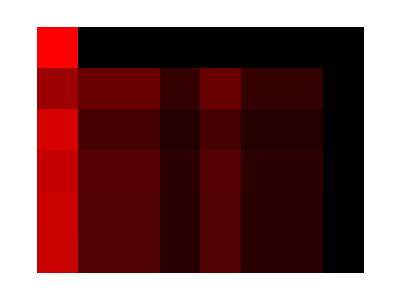

```mathematica
QuantumCellularAutomata2[{operatorHadamard},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],5]
```

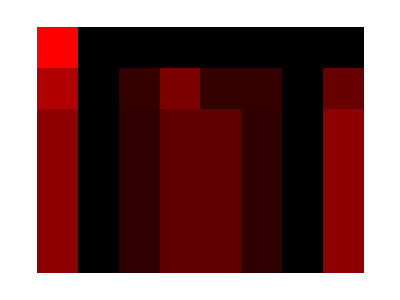

```mathematica
QuantumCellularAutomata2[{operatorCNOT},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],5]
```

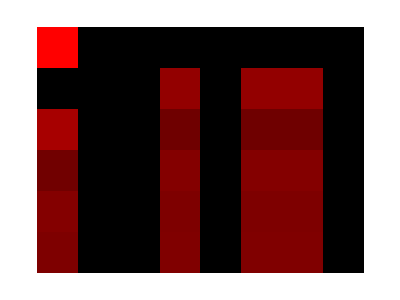

```mathematica
QuantumCellularAutomata2[{operatorPauliX},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],5]
```

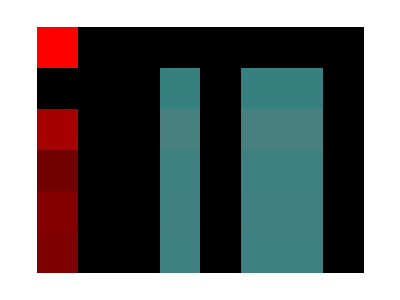

```mathematica
QuantumCellularAutomata2[{operatorPauliY},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],5]
```

```mathematica
Rotate[QuantumCellularAutomata2[{operatorSqrtNOT},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],100],Pi/2]
```

-Graphics-

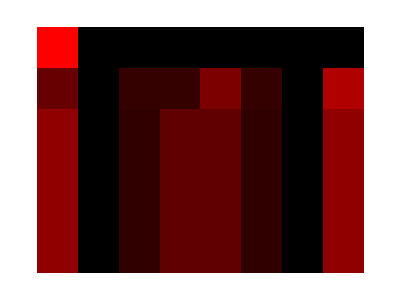

```mathematica
QuantumCellularAutomata2[{operatorPauliX,operatorCNOT},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],5]
```

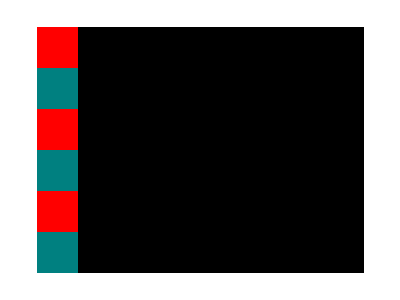

```mathematica
QuantumCellularAutomata2[{operatorPauliX,operatorPauliY},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],5]
```

```mathematica
Rotate[QuantumCellularAutomata2[{operatorHadamard,operatorRotate[Pi/4],operatorCNOT},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],500],Pi/2]
```

-Graphics-

```mathematica
Rotate[QuantumCellularAutomata2[{operatorRotate[Pi/4]},QuantumFiniteDimensionalState[{{1/2,-I},{-1,1/4},{I,0},{1,0}}],500],Pi/2]
```

-Graphics-

```mathematica
Rotate[QuantumCellularAutomata2[{operatorCNOT,operatorHadamard,operatorRotate[Pi/4]},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0},{1,0}}],500],Pi/2]
```

-Graphics-

```mathematica
Rotate[QuantumCellularAutomata2[{operatorCNOT,operatorRotate[Pi/4],operatorHadamard},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0},{1,0}}],500],Pi/2]
```

-Graphics-

```mathematica
Rotate[QuantumCellularAutomata2[{operatorRotate[Pi/4],operatorHadamard,operatorCNOT},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0},{1,0}}],500],Pi/2]
```

-Graphics-

```mathematica
Rotate[QuantumCellularAutomata2[{operatorHadamard,operatorRotate[Pi/4],operatorCNOT},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0},{1,0}}],500],Pi/2]
```

-Graphics-

```mathematica
Rotate[QuantumCellularAutomata2[{random},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0},{1,0}}],500],Pi/2]
```

-Graphics-

```mathematica
separateStates[states_]:= Map[Normal[#["StateVector"]]&,states]
separateAllStates[states_]:= separateStates[#]&/@states
```

```mathematica
plotNorms[matrices_,initialstate_,steps_]:= ListLinePlot[Transpose@(Map[Norm[#]^2&,separateStates[evolutionQCA2[matrices,initialstate,steps]],{2}]),PlotLegends-> {"000","001","010","011","100","101","110","111"},PlotRange->All]
```

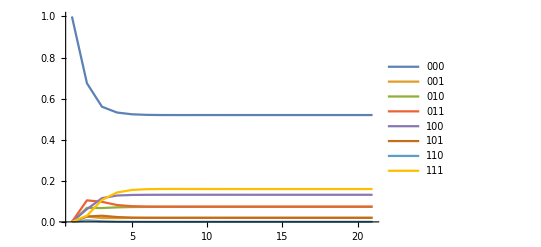

```mathematica
plotNorms[{operatorCNOT,operatorHadamard,operatorRotate,operatorHadamard},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],20]
```

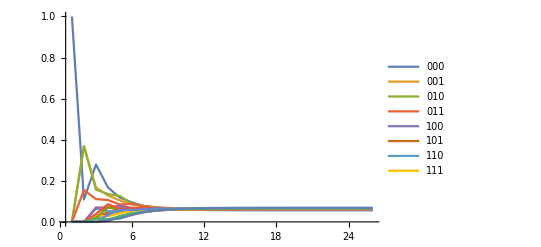

```mathematica
plotNorms[{random},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0},{1,0}}],25]
```

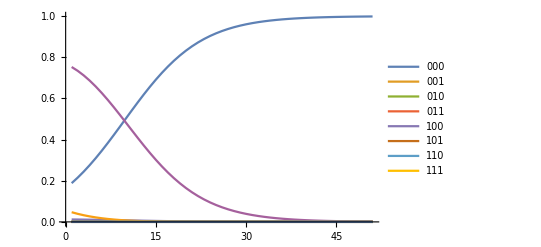

```mathematica
plotNorms[{operatorRotate[Pi/4]},QuantumFiniteDimensionalState[{{1/2,-I},{-1,1/4},{I,0},{1,0}}],50]
```